## 3D Gauß

```mathematica
Assuming[{α>0, β>0, γ> 0},FullSimplify[FourierTransform[((2/π)^(3/4)*1/(√(α β γ))ⅇ^(-x^2/α^2-y^2/β^2-z^2/γ^2))^2,{x,y,z},{u,v,w}, FourierParameters->{1, -1}]]]
```

ⅇ^(1/8 (-u^2 α^2-v^2 β^2-w^2 γ^2))

## 1D parabola with heaviside

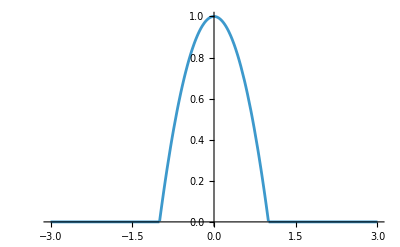

```mathematica
Plot[(-x^2+1)*HeavisideTheta[x+1]*HeavisideTheta[1-x],{x, -3, 3}]
```

```mathematica
FullSimplify[FourierTransform[((-x^2+1)*HeavisideTheta[x+1]*HeavisideTheta[1-x])^2, x, k, FourierParameters->{1, -1}]]
```

-(16 (3 k Cos[k]+(-3+k^2) Sin[k]))/k^5

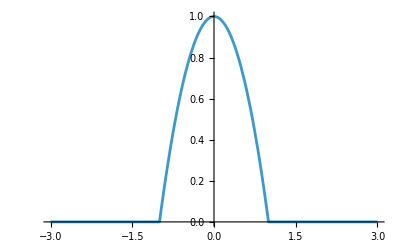

```mathematica
Plot[(-x^2+1)*HeavisideTheta[-x^2+1],{x, -3, 3}]
```

```mathematica
FullSimplify[FourierTransform[((-x^2+1)*HeavisideTheta[-x^2+1])^2, x, k, FourierParameters->{1, -1}]]
```

-(16 (3 k Cos[k]+(-3+k^2) Sin[k]))/k^5

## 3D parabola with heaviside

```mathematica
Manipulate[ContourPlot3D[(1 - x^2/a-y^2/b-z^2/c)*HeavisideTheta[1 - x^2/a-y^2/b-z^2/c]==.7, {x, -3,3},{y, -3,3}, {z, -3,3} ],{a, 1,3}, {b, 1, 3}, {c, 1, 3}]
```

```mathematica
FullSimplify[FourierTransform[((1 - x^2/a-y^2/b-z^2/c)*HeavisideTheta[1 - x^2/a-y^2/b-z^2/c])^2,{x,y,z},{u,v,w},FourierParameters->{1, -1}]]
```

```mathematica
FullSimplify[15/(2 R^3)∫_0^R r/k(1-r^2/R^2)Sin[k r]ⅆr]
```

-(15 (3 k R Cos[k R]+(-3+k^2 R^2) Sin[k R]))/(k^5 R^5)

```mathematica
FullSimplify[(-4π 225 A)/αβγ∫_0^∞ 1/k^8((3-k^2)Sin[k]-3k Cos[k])^2 ⅆk]
```

-(60 A π^2)/(7 αβγ)

```mathematica
FullSimplify[(675 A)/αβγ∫_0^∞ 1/k^8((3-k^2)Sin[k]-3k Cos[k])^2 ⅆk]
```

(45 A π)/(7 αβγ)

```mathematica
∫_0^∞ 1/k^8((3-k^2)Sin[k]-3k Cos[k])^2 ⅆk
```

π/105